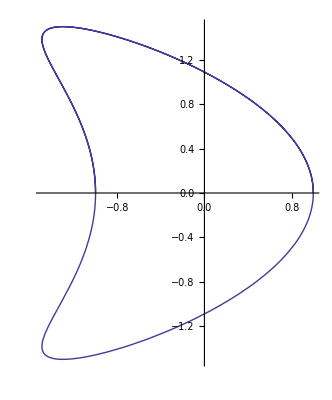

```mathematica
ParametricPlot[{a Cos[t]+0.5b (Cos[2 t]-1),c Sin[ t]}/.{a->1,b->1.3,c->1.5},{t,0,3*π}]
```

```mathematica
A-wigth
D - height
C-offset
ArcTan
```

```mathematica
D[(1.5Sin[t])/(Cos[t]+0.67(Cos[2 t]-1)),t]/.t->π-1e-10
```

-(1.5 Cos[10+e])/(-Cos[10+e]+0.67 (-1+Cos[2 (-10-e+π)]))-(1.5 Sin[10+e] (-Sin[10+e]-1.34 Sin[2 (-10-e+π)]))/(-Cos[10+e]+0.67 (-1+Cos[2 (-10-e+π)]))^2

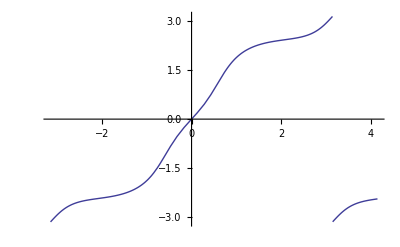

```mathematica
Plot[Arg[Cos[t]+0.67(Cos[2 t]-1)+ⅈ 1.5Sin[t]],{t,-π,π+1}]
```

```mathematica
Cos[2t]==2 Cos[t]^2-1//Simplify
```

True

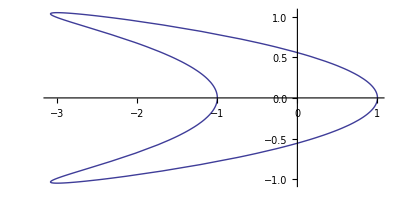

```mathematica
ParametricPlot[{a Cos[t]+b (Cos[t]^2-1),d Sin[ t]}/.{a->1,b->3,c->-0.65,d->1.05},{t,0,2*π}]
```

```mathematica
a Cos[t]+0.5b (Cos[2 t]-1)//TrigReduce
```

-0.5 b+a Cos[t]+0.5 b Cos[2 t]

```mathematica
(Cos[t/2]^2+Sin[t/2]^2)^(1/2)//Simplify
```

1

```mathematica
Sin[t/2+π/4]//TrigExpand
```

Cos[t/2]/(√2)+Sin[t/2]/(√2)

```mathematica
1./√2
```

0.707107

```mathematica
((Cos[t/2]+Sin[t/2])/(√2))^20==0//Reduce
```

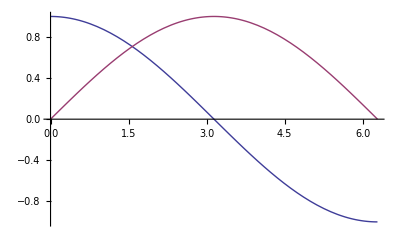

```mathematica
Plot[{Cos[t/2],Sin[t/2]},{t,0,2*π},PlotRange->Full]
```

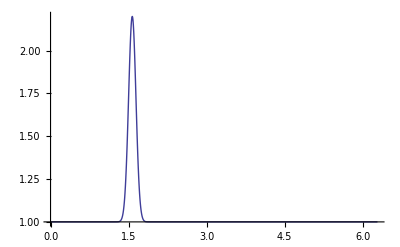

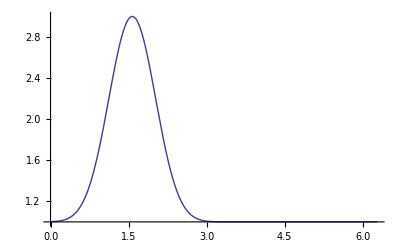

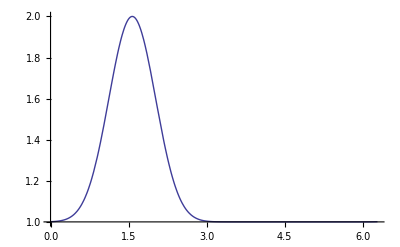

```mathematica
Plot[(1+0.6(1-Tanh[100(t-π)])Sin[t]^200),{t,0,2*π},PlotRange->Full]
Plot[1+2((Sin[t/2]+Cos[t/2])/(√2))^20,{t,0,2*π},PlotRange->Full]
Plot[(1+((Cos[t/2]+Sin[t/2])/(√2))^20),{t,0,2*π},PlotRange->Full]
```

```mathematica
1.8/5 Sin[t](1+((Cos[t/2]+Sin[t/2])/(√2))^200)/.t->3π/4
```

0.254558

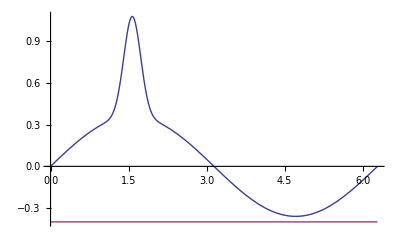

```mathematica
Plot[{1.8/5 Sin[t](1+2((Cos[t/2]+Sin[t/2])/(√2))^150),-0.4},{t,0,2*π},PlotRange->Full]
```

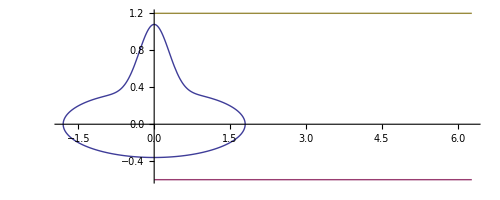

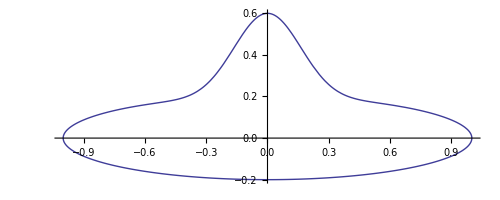

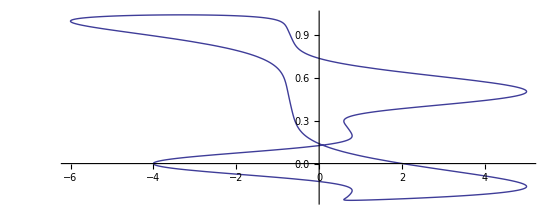

```mathematica
(*ParametricPlot[{Cos[t],1/5 Sin[t](1+2 Sin[t/2+π/4]^200)},{t,0,2*π}]*)
ParametricPlot[{{1.8Cos[t],1.8/5 Sin[t](1+2((Cos[t/2]+Sin[t/2])/(√2))^150)},{t,-0.6},{t,1.2}},{t,0,2*π}]
ParametricPlot[{1Cos[t],1/5 Sin[t](1+2((Cos[t/2]+Sin[t/2])/(√2))^150)},{t,0,2*π}]
ParametricPlot[{1Cos[t]-5 Cos[2t]^5,1/3 Sin[t]+Sin[t/2]^5},{t,0,2*π}]
```

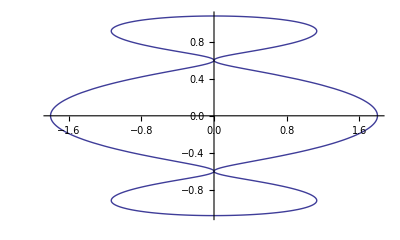

```mathematica
ParametricPlot[{Cos[t]+0.8Cos[5t],Sin[t]+0.08Sin[5t]},{t,0,2π},PlotRange->Full]
```

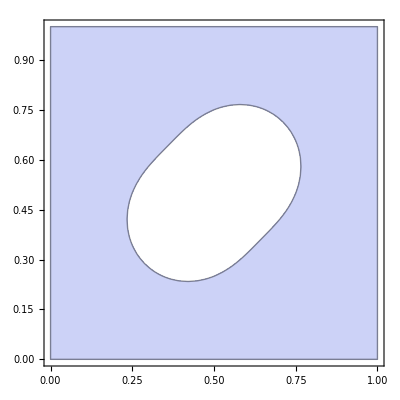

```mathematica
RegionPlot[√((x-Subscript[x, 0])^2+(y-Subscript[y, 0])^2)-(Subscript[r, 0]+ϵ Sin[2Arg[(x-Subscript[x, 0])+ⅈ (y-Subscript[y, 0])]])>0/.{Subscript[x, 0]->0.5,Subscript[y, 0]->0.5,ϵ->0.05,Subscript[r, 0]->0.25},{x,0,1},{y,0,1}]
```

```mathematica
5
```

```mathematica
Cos[t]+Cos[4 t]//FullSimplify
```

Cos[t]+Cos[4 t]

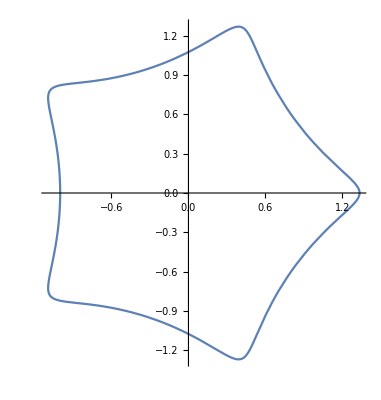

```mathematica
ParametricPlot[1/6{ 7Sin[t]+Cos[4t],7Cos[t]+Sin[4t]},{t,0,2π},PlotRange->Full]
```

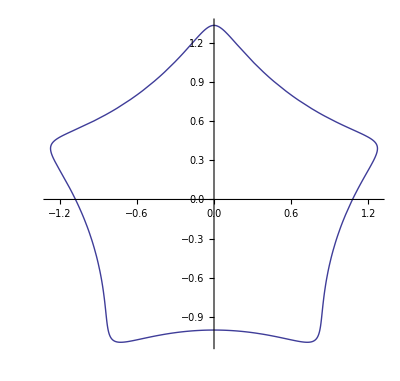

```mathematica
ParametricPlot[1/6{ 7Cos[t]+Sin[4t],7Sin[t]+Cos[4t]},{t,0,2π},PlotRange->Full]
```

```mathematica
7
```

```mathematica
3
```

```mathematica
fx=cos(u)*(abs(cos(1*u/4))^0.5+abs(sin(1*u/4))^0.5)^(-1/0.3)
fy=cos(u)*sin(v)*(abs(cos(1*u/4))^0.5+abs(sin(1*u/4))^0.5)^(-1/0.3)*(abs(cos(5*v/4))^1.7+abs(sin(5*v/4))^1.7)^(-1/0.1)
```

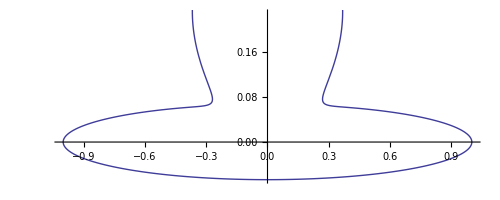

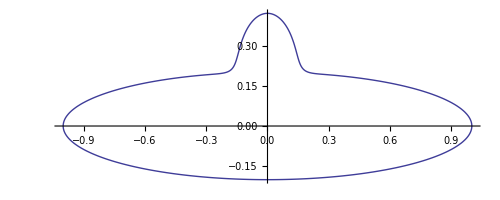

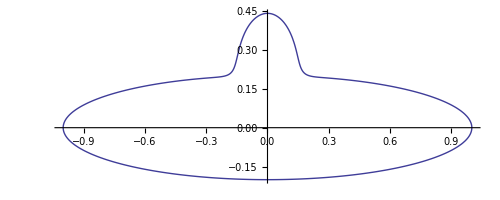

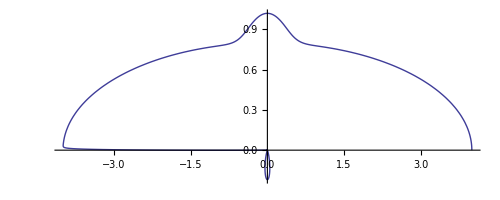

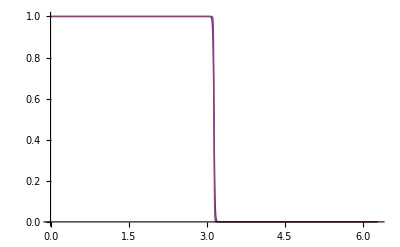

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
ParametricPlot[{Cos[t],1/15 Sin[t]}(1+5((Cos[t/2]+Sin[t/2])/(√2))^500),{t,0,2*π}]
ParametricPlot[{Cos[t],1/5 Sin[t]}(1+1.1(1/(ⅇ^(100(t-π))+1))Sin[t]^200),{t,0,2*π}]
ParametricPlot[{Cos[t],1/5 Sin[t]}(1+0.6(1-Tanh[100(t-π)])Sin[t]^200),{t,0,2*π}]
ParametricPlot[{Cos[t],1/5 Sin[t]}(2(1-Tanh[100(t-π)])+1.1 Sin[t]^200),{t,0,2*π}]
Plot[{1/(ⅇ^(100(t-π))+1),1/2-1/2Tanh[100(t-π)]},{t,0,2*π}]
```

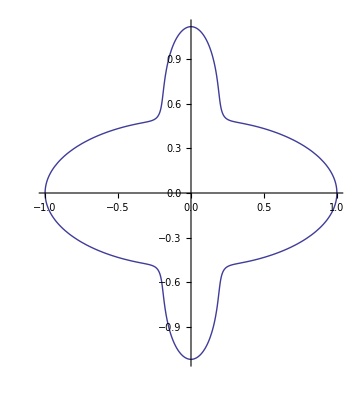

```mathematica
ParametricPlot[{Cos[t],Sin[t]}√((1+4 Sin[t]^40)/(Cos[t]^2+4 Sin[t]^2)),{t,0,2*π}]
```

```mathematica
{Cos[t],1/5 Sin[t]}(1+1.1(1/(ⅇ^(100(t-π))+1))Sin[t]^200)//Simplify
```

{Cos[t] (1+(1.1 Sin[t]^200)/(1+ⅇ^(100 (-π+t)))),1/5 (Sin[t]+(1.1 Sin[t]^201)/(1+ⅇ^(100 (-π+t))))}

```mathematica
Cos[t] Sin[t]^200//FullSimplify
```

Cos[t] Sin[t]^200

```mathematica
1.1(1/(ⅇ^(100(t-π))+1))==1//Reduce
```

ⅇ^(100 t)==2.73927×10^135

```mathematica
f(t) = (1+c sin(t)^p/(d exp(e(t-pi))+1))
x=a cos(t)f(t)
y=b sin(t)f(t)
```

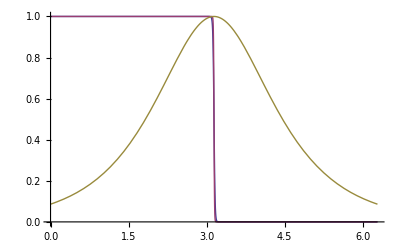

```mathematica
Plot[{1/(ⅇ^(100(t-π))+1),1/2-1/2Tanh[100(t-π)],Sech[ (-π+t)]},{t,0,2*π}]
```

```mathematica
u=.
```

```mathematica
a^2 √a
```

a^(5/2)

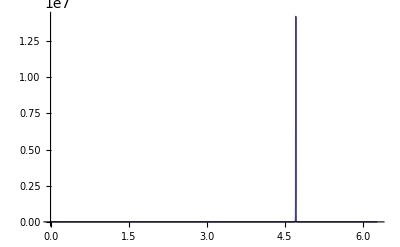

```mathematica
Plot[Cos[π/4+t/a]^2/Sin[π/4+t/a]^2/.a->2,{t,0,2*π},PlotRange->Full]
```

```mathematica
u=(1+c ((Cos[t/a]+Sin[t/a])/(√a))^p)
(**)(*u=(1+a Sin[t/a+π/4]^p)*)
D[u,t]
D[u,{t,2}]
D[u,{t,3}]
D[u,{t,4}]
D[u,{t,5}]
```

1+c ((Cos[t/a]+Sin[t/a])/(√a))^p

(c p ((Cos[t/a]+Sin[t/a])/(√a))^(-1+p) (Cos[t/a]/a-Sin[t/a]/a))/(√a)

c ((p ((Cos[t/a]+Sin[t/a])/(√a))^(-1+p) (-Cos[t/a]/a^2-Sin[t/a]/a^2))/(√a)+((-1+p) p ((Cos[t/a]+Sin[t/a])/(√a))^(-2+p) (Cos[t/a]/a-Sin[t/a]/a)^2)/a)

c ((p ((Cos[t/a]+Sin[t/a])/(√a))^(-1+p) (-Cos[t/a]/a^3+Sin[t/a]/a^3))/(√a)+(3 (-1+p) p ((Cos[t/a]+Sin[t/a])/(√a))^(-2+p) (-Cos[t/a]/a^2-Sin[t/a]/a^2) (Cos[t/a]/a-Sin[t/a]/a))/a+((-2+p) (-1+p) p ((Cos[t/a]+Sin[t/a])/(√a))^(-3+p) (Cos[t/a]/a-Sin[t/a]/a)^3)/a^(3/2))

c ((p ((Cos[t/a]+Sin[t/a])/(√a))^(-1+p) (Cos[t/a]/a^4+Sin[t/a]/a^4))/(√a)+(3 (-1+p) p ((Cos[t/a]+Sin[t/a])/(√a))^(-2+p) (-Cos[t/a]/a^2-Sin[t/a]/a^2)^2)/a+(4 (-1+p) p ((Cos[t/a]+Sin[t/a])/(√a))^(-2+p) (-Cos[t/a]/a^3+Sin[t/a]/a^3) (Cos[t/a]/a-Sin[t/a]/a))/a+(6 (-2+p) (-1+p) p ((Cos[t/a]+Sin[t/a])/(√a))^(-3+p) (-Cos[t/a]/a^2-Sin[t/a]/a^2) (Cos[t/a]/a-Sin[t/a]/a)^2)/a^(3/2)+((-3+p) (-2+p) (-1+p) p ((Cos[t/a]+Sin[t/a])/(√a))^(-4+p) (Cos[t/a]/a-Sin[t/a]/a)^4)/a^2)

c ((p ((Cos[t/a]+Sin[t/a])/(√a))^(-1+p) (Cos[t/a]/a^5-Sin[t/a]/a^5))/(√a)+(10 (-1+p) p ((Cos[t/a]+Sin[t/a])/(√a))^(-2+p) (-Cos[t/a]/a^3+Sin[t/a]/a^3) (-Cos[t/a]/a^2-Sin[t/a]/a^2))/a+(5 (-1+p) p ((Cos[t/a]+Sin[t/a])/(√a))^(-2+p) (Cos[t/a]/a^4+Sin[t/a]/a^4) (Cos[t/a]/a-Sin[t/a]/a))/a+(15 (-2+p) (-1+p) p ((Cos[t/a]+Sin[t/a])/(√a))^(-3+p) (-Cos[t/a]/a^2-Sin[t/a]/a^2)^2 (Cos[t/a]/a-Sin[t/a]/a))/a^(3/2)+(10 (-2+p) (-1+p) p ((Cos[t/a]+Sin[t/a])/(√a))^(-3+p) (-Cos[t/a]/a^3+Sin[t/a]/a^3) (Cos[t/a]/a-Sin[t/a]/a)^2)/a^(3/2)+(10 (-3+p) (-2+p) (-1+p) p ((Cos[t/a]+Sin[t/a])/(√a))^(-4+p) (-Cos[t/a]/a^2-Sin[t/a]/a^2) (Cos[t/a]/a-Sin[t/a]/a)^3)/a^2+((-4+p) (-3+p) (-2+p) (-1+p) p ((Cos[t/a]+Sin[t/a])/(√a))^(-5+p) (Cos[t/a]/a-Sin[t/a]/a)^5)/a^(5/2))

```mathematica
(*u=1+c(1/(d ⅇ^(e(t-π))+1))Sin[t]^p*)
u=1+c Sf[t] Sin[t]^p
D[u,t]
D[u,{t,2}]== (-1+p) p c Sf[t] Cos[t]^2 Sin[t]^(-2+p)+2 c p Cos[t] Sin[t]^(-1+p) Sf'[t]+c Sin[t]^p Sf''[t]-p (u-1)//Simplify
D[u,{t,3}]
D[u,{t,4}]
D[u,{t,5}]
```

1+c Sf[t] Sin[t]^p

c p Cos[t] Sf[t] Sin[t]^(-1+p)+c Sin[t]^p Sf'[t]

True

c Sf[t] ((-2+p) (-1+p) p Cos[t]^3 Sin[t]^(-3+p)-2 (-1+p) p Cos[t] Sin[t]^(-1+p)-p^2 Cos[t] Sin[t]^(-1+p))+3 c ((-1+p) p Cos[t]^2 Sin[t]^(-2+p)-p Sin[t]^p) Sf'[t]+3 c p Cos[t] Sin[t]^(-1+p) Sf''[t]+c Sin[t]^p Sf^(3)[t]

c Sf[t] ((-3+p) (-2+p) (-1+p) p Cos[t]^4 Sin[t]^(-4+p)-3 (-2+p) (-1+p) p Cos[t]^2 Sin[t]^(-2+p)-2 (-1+p)^2 p Cos[t]^2 Sin[t]^(-2+p)-(-1+p) p^2 Cos[t]^2 Sin[t]^(-2+p)+2 (-1+p) p Sin[t]^p+p^2 Sin[t]^p)+4 c ((-2+p) (-1+p) p Cos[t]^3 Sin[t]^(-3+p)-2 (-1+p) p Cos[t] Sin[t]^(-1+p)-p^2 Cos[t] Sin[t]^(-1+p)) Sf'[t]+6 c ((-1+p) p Cos[t]^2 Sin[t]^(-2+p)-p Sin[t]^p) Sf''[t]+4 c p Cos[t] Sin[t]^(-1+p) Sf^(3)[t]+c Sin[t]^p Sf^(4)[t]

c Sf[t] ((-4+p) (-3+p) (-2+p) (-1+p) p Cos[t]^5 Sin[t]^(-5+p)-4 (-3+p) (-2+p) (-1+p) p Cos[t]^3 Sin[t]^(-3+p)-3 (-2+p)^2 (-1+p) p Cos[t]^3 Sin[t]^(-3+p)-2 (-2+p) (-1+p)^2 p Cos[t]^3 Sin[t]^(-3+p)-(-2+p) (-1+p) p^2 Cos[t]^3 Sin[t]^(-3+p)+6 (-2+p) (-1+p) p Cos[t] Sin[t]^(-1+p)+4 (-1+p)^2 p Cos[t] Sin[t]^(-1+p)+4 (-1+p) p^2 Cos[t] Sin[t]^(-1+p)+p^3 Cos[t] Sin[t]^(-1+p))+5 c ((-3+p) (-2+p) (-1+p) p Cos[t]^4 Sin[t]^(-4+p)-3 (-2+p) (-1+p) p Cos[t]^2 Sin[t]^(-2+p)-2 (-1+p)^2 p Cos[t]^2 Sin[t]^(-2+p)-(-1+p) p^2 Cos[t]^2 Sin[t]^(-2+p)+2 (-1+p) p Sin[t]^p+p^2 Sin[t]^p) Sf'[t]+10 c ((-2+p) (-1+p) p Cos[t]^3 Sin[t]^(-3+p)-2 (-1+p) p Cos[t] Sin[t]^(-1+p)-p^2 Cos[t] Sin[t]^(-1+p)) Sf''[t]+10 c ((-1+p) p Cos[t]^2 Sin[t]^(-2+p)-p Sin[t]^p) Sf^(3)[t]+5 c p Cos[t] Sin[t]^(-1+p) Sf^(4)[t]+c Sin[t]^p Sf^(5)[t]

```mathematica
(c d e ⅇ^(e (-π+t)) Sin[t]^p)/((1+d ⅇ^(e (-π+t)))^2)==(d e ⅇ^(e (-π+t)))/(1+d ⅇ^(e (-π+t)))(u-1)//Simplify
(c p Cos[t] Sin[t]^(-1+p))/(1+d ⅇ^(e (-π+t)))==p Cot[t](u-1)
```

True

True

```mathematica
(p Cot[t]+(d e ⅇ^(e (-π+t)))/(1+d ⅇ^(e (-π+t))))//FullSimplify
```

(d e ⅇ^(e t))/(ⅇ^(e π)+d ⅇ^(e t))+p Cot[t]

```mathematica
Cos[t]/Sin[t]
```

Cot[t]

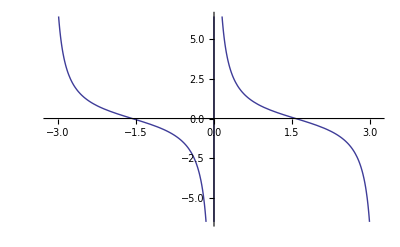

```mathematica
Plot[Cot[t],{t,-π,π}]
```

```mathematica
-4/5+4/12-5/3//N
```

-2.13333

```mathematica
1.1/2
```

0.55

```mathematica
-4 e^4 Sech[e (-π+t)]^4(1-2u)== 8 e/d D[u,t]D[u,{t,2}]
```

True

```mathematica
u=(1-d Tanh[e(t-π)])/2
D[u,t]
D[u,{t,2}]==-2 e/d D[u,t] (1-2u)//Simplify
D[u,{t,3}]== 4 e/d D[u,t]^2- 2 e/d  D[u,{t,2}](1-2u)//Simplify
D[u,{t,4}]==12 e/d  D[u,{t,2}]D[u,t]- 2 e/d  D[u,{t,3}](1-2u)//Simplify
D[u,{t,5}]==16 e/d  D[u,{t,3}]D[u,t]+12 e/d  D[u,{t,2}]^2- 2 e/d  D[u,{t,4}](1-2u)//Simplify
```

1/2 (1-d Tanh[e (-π+t)])

-1/2 d e Sech[e (-π+t)]^2

True

True

True

«1 more identical outputs»

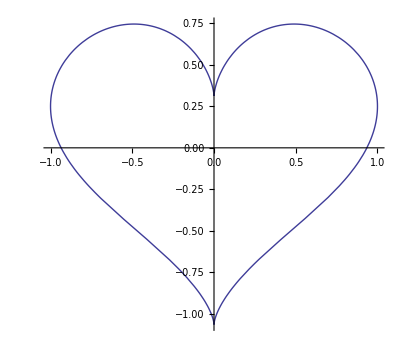

```mathematica
ParametricPlot[1/16{ 16 Sin[t]^3,13 Cos[t]-5 Cos[2 t]-2Cos[3t]-Cos[4t]},{t,0,2π}]
```

```mathematica
13 Cos[t]-5 Cos[2 t]-2Cos[3t]-Cos[4t]//TrigFactor
```

13 Cos[t]-5 Cos[2 t]-2 Cos[3 t]-Cos[4 t]

```mathematica
D[f[r,t]/a[r,t],r]
```

-(f[r,t] a^(1,0)[r,t])/a[r,t]^2+(f^(1,0)[r,t])/a[r,t]

```mathematica
x=f*Cosh[n]Cos[t]
y=f*Sinh[n]Sin[t]
D[x,{n,2}]==x
D[y,{n,2}]==y
```

f Cos[t] Cosh[n]

f Sin[t] Sinh[n]

True

True

```mathematica
1/s 1/(1−e^Ts z^(−1))
```

```mathematica
D[1/s 1/(1−ⅇ^Ts z^(−1)),{s,2}]
```

```mathematica
2/(s^3 (1-ⅇ^(s T)/z))+((2 ⅇ^(2 s T) T^2)/((1-ⅇ^(s T)/z)^3 z^2)+(ⅇ^(s T) T^2)/((1-ⅇ^(s T)/z)^2 z))/s-(2 ⅇ^(s T) T)/(s^2 (1-ⅇ^(s T)/z)^2 z)//Simplify
```

-(z (ⅇ^(2 s T) (2+2 s T+s^2 T^2)+ⅇ^(s T) (-4-2 s T+s^2 T^2) z+2 z^2))/(s^3 (ⅇ^(s T)-z)^3)

```mathematica
u=e(5+Cos[c x+d y])
D[u,y]
D[u,{x,2}]
D[u,{y,2}]
D[u,x,y]
```

e (5+Cos[c x+d y])

-d e Sin[c x+d y]

-c^2 e Cos[c x+d y]

-d^2 e Cos[c x+d y]

-c d e Cos[c x+d y]

```mathematica
D[(2 c'[y]d[x] Cos[y d[x]]+ Sin[y d[x]] c''[y])x Cos[x c[y]],y]+x^2 c'[y] c''[y]u==(x  Derivative[3][c][y]-2 x  d[x]^2 c'[y])Cos[x c[y]] Sin[y d[x]]-2 x^2 Cos[y d[x]] d[x] Sin[x c[y]] c'[y]^2+3 x Cos[x c[y]] Cos[y d[x]] d[x] c''[y]//Simplify
```

True

```mathematica
-2 x Cos[x c[y]] d[x]^2 Sin[y d[x]] c'[y]-2 x^2 Cos[y d[x]] d[x] Sin[x c[y]] c'[y]^2+3 x Cos[x c[y]] Cos[y d[x]] d[x] c''[y]-x^2 Sin[x c[y]] Sin[y d[x]] c'[y] c''[y]+x Cos[x c[y]] Sin[y d[x]] Derivative[3][c][y]
```

```mathematica
D[u,x,y]==-(x c[y] c'[y]+y d[x] d'[x])u+(c[y] d[x]+x y  c'[y] d'[x])Cos[x c[y]] Cos[y d[x]]+Cos[x c[y]] Sin[y d[x]] c'[y]+Sin[x c[y]]Cos[y d[x]]  d'[x]//FullSimplify
```

True

```mathematica
c[y] Cos[x c[y]] Cos[y d[x]] d[x]+Cos[x c[y]] Sin[y d[x]] c'[y]-x c[y] Sin[x c[y]] Sin[y d[x]] c'[y]+Cos[y d[x]] Sin[x c[y]] d'[x]-y d[x] Sin[x c[y]] Sin[y d[x]] d'[x]+x y Cos[x c[y]] Cos[y d[x]] c'[y] d'[x]
```

```mathematica
u=Sin[c[y]x]Sin[d[x]y]
D[u,{x,1}]
D[u,{y,1}]
D[u,x,y]==-(x c[y] c'[y]+y d[x] d'[x])u+(c[y] d[x]+x y  c'[y] d'[x])Cos[x c[y]] Cos[y d[x]]+Cos[x c[y]] Sin[y d[x]] c'[y]+Sin[x c[y]]Cos[y d[x]]  d'[x]//FullSimplify
D[u,{x,2}]==-(c[y]^2 +y^2 d'[x]^2)u+(2  c[y] d'[x]Cos[x c[y]]+Sin[x c[y]] d''[x])y Cos[y d[x]]//Simplify
D[u,{y,2}]==-(d[x]^2 +x^2 c'[y]^2)u+ (2 c'[y]d[x] Cos[y d[x]]+ Sin[y d[x]] c''[y])x Cos[x c[y]]//Simplify
D[u,{x,2},y]==-(2 c[y] c'[y]+2 y d'[x]^2+y d[x] d''[x])u-(c[y]^2 +y^2 d'[x]^2)D[u,{y,1}]+(2 c[y]  d'[x]+2 y  c'[y] d'[x]+x y c'[y] d''[x])Cos[x c[y]] Cos[y d[x]] +( d''[x]-2 x y c[y] c'[y] d'[x])Cos[y d[x]] Sin[x c[y]]-2 y c[y] Cos[x c[y]] d[x] Sin[y d[x]] d'[x]//Simplify
D[u,{y,2},x]==- (2x c'[y]^2+2d[x] d'[x]+x c[y]c''[y])u-(d[x]^2 +x^2 c'[y]^2)D[u,{x,1}]+(2 d[x] c'[y]+2 x c'[y] d'[x]+x y  d'[x] c''[y])Cos[x c[y]] Cos[y d[x]]+( c''[y]-2 x y d[x] c'[y] d'[x])Cos[x c[y]] Sin[y d[x]]-2 x c[y] c'[y]d[x]Sin[x c[y]]Cos[y d[x]]//Simplify
D[u,{x,3}]==-3 y^2 d'[x] d''[x]u-(c[y]^2 +y^2 d'[x]^2)D[u,{x,1}]+(y  Derivative[3][d][x]-2 y c[y]^2  d'[x])Cos[y d[x]] Sin[x c[y]]+3 y c[y] Cos[x c[y]] Cos[y d[x]] d''[x]-2 y^2 c[y] Cos[x c[y]] Sin[y d[x]] d'[x]^2//Simplify
D[u,{y,3}]==-3 x^2 c'[y] c''[y]u-(d[x]^2 +x^2 c'[y]^2)D[u,{y,1}]+ (x  Derivative[3][c][y]-2 x  d[x]^2 c'[y])Cos[x c[y]] Sin[y d[x]]-2 x^2 Cos[y d[x]] d[x] Sin[x c[y]] c'[y]^2+3 x Cos[x c[y]] Cos[y d[x]] d[x] c''[y]//Simplify
```

Sin[x c[y]] Sin[y d[x]]

c[y] Cos[x c[y]] Sin[y d[x]]+y Cos[y d[x]] Sin[x c[y]] d'[x]

Cos[y d[x]] d[x] Sin[x c[y]]+x Cos[x c[y]] Sin[y d[x]] c'[y]

c[y] Cos[x c[y]] Cos[y d[x]] d[x]+Cos[x c[y]] Sin[y d[x]] c'[y]-x c[y] Sin[x c[y]] Sin[y d[x]] c'[y]+Cos[y d[x]] Sin[x c[y]] d'[x]-y d[x] Sin[x c[y]] Sin[y d[x]] d'[x]+x y Cos[x c[y]] Cos[y d[x]] c'[y] d'[x]

True

True

True

«3 more identical outputs»

```mathematica
D[u[x,y],{y,1}]
```

u^(0,1)[x,y]

```mathematica
-(x c[y] c'[y]+y d[x] d'[x])u+(c[y] d[x]+x y  c'[y] d'[x])Cos[x c[y]] Cos[y d[x]]+Cos[x c[y]] Sin[y d[x]] c'[y]+Sin[x c[y]]Cos[y d[x]]  d'[x]/.{c[y]->c, c'[y]->cy,d'[x]->dx,d[x]->d, d''[x]->dxx,Derivative[0,1][u][x,y]->uy}

-(2 c[y] c'[y]+2 y d'[x]^2+y d[x] d''[x])u-(c[y]^2 +y^2 d'[x]^2)Derivative[0,1][u][x,y]+(2 c[y]  d'[x]+2 y  c'[y] d'[x]+x y c'[y] d''[x])Cos[x c[y]] Cos[y d[x]] +( d''[x]-2 x y c[y] c'[y] d'[x])Cos[y d[x]] Sin[x c[y]]-2 y c[y] Cos[x c[y]] d[x] Sin[y d[x]] d'[x]/.{c[y]->c, c'[y]->cy,d'[x]->dx,d[x]->d, d''[x]->dxx,Derivative[0,1][u][x,y]->uy}

- (2x c'[y]^2+2d[x] d'[x]+x c[y]c''[y])u-(d[x]^2 +x^2 c'[y]^2)D[u,{x,1}]+(2 d[x] c'[y]+2 x c'[y] d'[x]+x y  d'[x] c''[y])Cos[x c[y]] Cos[y d[x]]+( c''[y]-2 x y d[x] c'[y] d'[x])Cos[x c[y]] Sin[y d[x]]-2 x c[y] c'[y]d[x]Sin[x c[y]]Cos[y d[x]]/.{c[y]->c, c'[y]->cy,d'[x]->dx,d[x]->d, d''[x]->dxx,Derivative[0,1][u][x,y]->uy,c''[y]->cyy,d''[y]->dyy}

-3 y^2 d'[x] d''[x]u-(c[y]^2 +y^2 d'[x]^2)D[u,{x,1}]+(y  Derivative[3][d][x]-2 y c[y]^2  d'[x])Cos[y d[x]] Sin[x c[y]]+3 y c[y] Cos[x c[y]] Cos[y d[x]] d''[x]-2 y^2 c[y] Cos[x c[y]] Sin[y d[x]] d'[x]^2/.{c[y]->c, c'[y]->cy,d'[x]->dx,d[x]->d, d''[x]->dxx,Derivative[0,1][u][x,y]->uy,c''[y]->cyy,d''[y]->dyy,Derivative[3][d][x]->d3x}

-3 x^2 c'[y] c''[y]u-(d[x]^2 +x^2 c'[y]^2)D[u,{y,1}]+ (x  Derivative[3][c][y]-2 x  d[x]^2 c'[y])Cos[x c[y]] Sin[y d[x]]-2 x^2 Cos[y d[x]] d[x] Sin[x c[y]] c'[y]^2+3 x Cos[x c[y]] Cos[y d[x]] d[x] c''[y]/.{c[y]->c, c'[y]->cy,d'[x]->dx,d[x]->d, d''[x]->dxx,Derivative[0,1][u][x,y]->uy,c''[y]->cyy,d''[y]->dyy,Derivative[3][d][x]->d3x,Derivative[3][c][y]->c3y}
```

(c d+cy dx x y) Cos[c x] Cos[d y]+dx Cos[d y] Sin[c x]+cy Cos[c x] Sin[d y]+(-c cy x-d dx y) Sin[c x] Sin[d y]

-uy (c^2+dx^2 y^2)+(2 c dx+2 cy dx y+cy dxx x y) Cos[c x] Cos[d y]+(dxx-2 c cy dx x y) Cos[d y] Sin[c x]-2 c d dx y Cos[c x] Sin[d y]+(-2 c cy-2 dx^2 y-d dxx y) Sin[c x] Sin[d y]

(2 cy d+2 cy dx x+cyy dx x y) Cos[c x] Cos[d y]-2 c cy d x Cos[d y] Sin[c x]+(cyy-2 cy d dx x y) Cos[c x] Sin[d y]+(-2 d dx-2 cy^2 x-c cyy x) Sin[c x] Sin[d y]-(d^2+cy^2 x^2) (dx y Cos[d y] Sin[c x]+c Cos[c x] Sin[d y])

3 c dxx y Cos[c x] Cos[d y]+(d3x y-2 c^2 dx y) Cos[d y] Sin[c x]-2 c dx^2 y^2 Cos[c x] Sin[d y]-3 dx dxx y^2 Sin[c x] Sin[d y]-(c^2+dx^2 y^2) (dx y Cos[d y] Sin[c x]+c Cos[c x] Sin[d y])

3 cyy d x Cos[c x] Cos[d y]-2 cy^2 d x^2 Cos[d y] Sin[c x]+(c3y x-2 cy d^2 x) Cos[c x] Sin[d y]-3 cy cyy x^2 Sin[c x] Sin[d y]-(d^2+cy^2 x^2) (d Cos[d y] Sin[c x]+cy x Cos[c x] Sin[d y])

```mathematica
u=.
```

```mathematica
D[a[x,y]D[u[x,y],x],x]
D[b[x,y]D[u[x,y],y],y]
```

a^(1,0)[x,y] u^(1,0)[x,y]+a[x,y] u^(2,0)[x,y]

b^(0,1)[x,y] u^(0,1)[x,y]+b[x,y] u^(0,2)[x,y]

```mathematica
F=D[a[x,y]D[u[x,y],x],x]+D[b[x,y]D[u[x,y],y],y]
D[F,x]/.{Derivative[0,2][u][x,y] ->uyy,Derivative[1,0][b][x,y]->bx,Derivative[0,1][b][x,y]->by,Derivative[0,1][u][x,y]->uy,Derivative[1,1][b][x,y]->bxy,Derivative[1,1][u][x,y]->uxy,Derivative[1,2][u][x,y]->uxyy,Derivative[1,0][a][x,y]->ax,Derivative[2,0][u][x,y]->uxx,Derivative[1,0][u][x,y] ->ux,Derivative[2,0][a][x,y]->axx,a[x,y]->a, Derivative[3,0][u][x,y]->u3x,b[x,y]->b}
D[F,y]/.{Derivative[0,2][u][x,y] ->uyy,Derivative[1,0][b][x,y]->bx,Derivative[0,1][b][x,y]->by,Derivative[0,1][u][x,y]->uy,Derivative[1,1][b][x,y]->bxy,Derivative[1,1][u][x,y]->uxy,Derivative[1,2][u][x,y]->uxyy,Derivative[1,0][a][x,y]->ax,Derivative[2,0][u][x,y]->uxx,Derivative[1,0][u][x,y] ->ux,Derivative[2,0][a][x,y]->axx,a[x,y]->a, Derivative[3,0][u][x,y]->u3x,b[x,y]->b,Derivative[0,1][a][x,y]->ay,Derivative[0,2][b][x,y]->byy, Derivative[0,3][u][x,y]->u3y,Derivative[1,1][a][x,y]->axy,Derivative[2,1][u][x,y]->uxxy}
```

b^(0,1)[x,y] u^(0,1)[x,y]+b[x,y] u^(0,2)[x,y]+a^(1,0)[x,y] u^(1,0)[x,y]+a[x,y] u^(2,0)[x,y]

a u3x+axx ux+2 ax uxx+by uxy+b uxyy+bxy uy+bx uyy

b u3y+axy ux+ay uxx+a uxxy+ax uxy+byy uy+2 by uyy

```mathematica
F=D[a[x,y]D[u[x,y],x],x]+D[b[x,y]D[u[x,y],y],y];
D[F,x]//FullSimplify
D[F,y]//FullSimplify
```

b^(1,1)[x,y] ((Sin[x c[y]] Sin[y d[x]])^(0,1)[x,y]+(Cos[y d[x]] d[x] Sin[x c[y]]+x Cos[x c[y]] Sin[y d[x]] c'[y])[x,y])+a^(2,0)[x,y] ((Sin[x c[y]] Sin[y d[x]])^(1,0)[x,y]+(c[y] Cos[x c[y]] Sin[y d[x]]+y Cos[y d[x]] Sin[x c[y]] d'[x])[x,y])+b^(0,1)[x,y] ((c[y] Cos[x c[y]] Sin[y d[x]]+y Cos[y d[x]] Sin[x c[y]] d'[x])^(0,1)[x,y]+(Cos[y d[x]] d[x] Sin[x c[y]]+x Cos[x c[y]] Sin[y d[x]] c'[y])^(1,0)[x,y]+(Sin[x c[y]] Sin[y d[x]])^(1,1)[x,y]+(Cos[y d[x]] (c[y] Cos[x c[y]] d[x]+(Sin[x c[y]]+x y Cos[x c[y]] c'[y]) d'[x])+Sin[y d[x]] (Cos[x c[y]] c'[y]-Sin[x c[y]] (x c[y] c'[y]+y d[x] d'[x])))[x,y])+b^(1,0)[x,y] (2 (Cos[y d[x]] d[x] Sin[x c[y]]+x Cos[x c[y]] Sin[y d[x]] c'[y])^(0,1)[x,y]+(Sin[x c[y]] Sin[y d[x]])^(0,2)[x,y]+(2 x Cos[x c[y]] Cos[y d[x]] d[x] c'[y]+Sin[y d[x]] (-Sin[x c[y]] (d[x]^2+x^2 c'[y]^2)+x Cos[x c[y]] c''[y]))[x,y])+b[x,y] (2 (Cos[y d[x]] (c[y] Cos[x c[y]] d[x]+(Sin[x c[y]]+x y Cos[x c[y]] c'[y]) d'[x])+Sin[y d[x]] (Cos[x c[y]] c'[y]-Sin[x c[y]] (x c[y] c'[y]+y d[x] d'[x])))^(0,1)[x,y]+(c[y] Cos[x c[y]] Sin[y d[x]]+y Cos[y d[x]] Sin[x c[y]] d'[x])^(0,2)[x,y]+(2 x Cos[x c[y]] Cos[y d[x]] d[x] c'[y]+Sin[y d[x]] (-Sin[x c[y]] (d[x]^2+x^2 c'[y]^2)+x Cos[x c[y]] c''[y]))^(1,0)[x,y]+2 (Cos[y d[x]] d[x] Sin[x c[y]]+x Cos[x c[y]] Sin[y d[x]] c'[y])^(1,1)[x,y]+(Sin[x c[y]] Sin[y d[x]])^(1,2)[x,y]+(Sin[y d[x]] (-Cos[x c[y]] (c[y] (d[x]^2+x^2 c'[y]^2)+2 x y d[x] c'[y] d'[x]-c''[y])-Sin[x c[y]] (2 x c'[y]^2+2 d[x] d'[x]+x c[y] c''[y]))+Cos[y d[x]] (-Sin[x c[y]] (2 x c[y] d[x] c'[y]+y (d[x]^2+x^2 c'[y]^2) d'[x])+Cos[x c[y]] (2 c'[y] (d[x]+x d'[x])+x y d'[x] c''[y])))[x,y])+2 a^(1,0)[x,y] (2 (c[y] Cos[x c[y]] Sin[y d[x]]+y Cos[y d[x]] Sin[x c[y]] d'[x])^(1,0)[x,y]+(Sin[x c[y]] Sin[y d[x]])^(2,0)[x,y]+(-Sin[x c[y]] Sin[y d[x]] (c[y]^2+y^2 d'[x]^2)+y Cos[y d[x]] (2 c[y] Cos[x c[y]] d'[x]+Sin[x c[y]] d''[x]))[x,y])+a[x,y] (3 (-Sin[x c[y]] Sin[y d[x]] (c[y]^2+y^2 d'[x]^2)+y Cos[y d[x]] (2 c[y] Cos[x c[y]] d'[x]+Sin[x c[y]] d''[x]))^(1,0)[x,y]+3 (c[y] Cos[x c[y]] Sin[y d[x]]+y Cos[y d[x]] Sin[x c[y]] d'[x])^(2,0)[x,y]+(Sin[x c[y]] Sin[y d[x]])^(3,0)[x,y]+(-c[y] Cos[x c[y]] (Sin[y d[x]] (c[y]^2+3 y^2 d'[x]^2)-3 y Cos[y d[x]] d''[x])+y Sin[x c[y]] (-3 y Sin[y d[x]] d'[x] d''[x]+Cos[y d[x]] (-3 c[y]^2 d'[x]-y^2 d'[x]^3+d^(3)[x])))[x,y])

b^(0,2)[x,y] ((Sin[x c[y]] Sin[y d[x]])^(0,1)[x,y]+(Cos[y d[x]] d[x] Sin[x c[y]]+x Cos[x c[y]] Sin[y d[x]] c'[y])[x,y])+a^(1,1)[x,y] ((Sin[x c[y]] Sin[y d[x]])^(1,0)[x,y]+(c[y] Cos[x c[y]] Sin[y d[x]]+y Cos[y d[x]] Sin[x c[y]] d'[x])[x,y])+a^(1,0)[x,y] ((c[y] Cos[x c[y]] Sin[y d[x]]+y Cos[y d[x]] Sin[x c[y]] d'[x])^(0,1)[x,y]+(Cos[y d[x]] d[x] Sin[x c[y]]+x Cos[x c[y]] Sin[y d[x]] c'[y])^(1,0)[x,y]+(Sin[x c[y]] Sin[y d[x]])^(1,1)[x,y]+(Cos[y d[x]] (c[y] Cos[x c[y]] d[x]+(Sin[x c[y]]+x y Cos[x c[y]] c'[y]) d'[x])+Sin[y d[x]] (Cos[x c[y]] c'[y]-Sin[x c[y]] (x c[y] c'[y]+y d[x] d'[x])))[x,y])+2 b^(0,1)[x,y] (2 (Cos[y d[x]] d[x] Sin[x c[y]]+x Cos[x c[y]] Sin[y d[x]] c'[y])^(0,1)[x,y]+(Sin[x c[y]] Sin[y d[x]])^(0,2)[x,y]+(2 x Cos[x c[y]] Cos[y d[x]] d[x] c'[y]+Sin[y d[x]] (-Sin[x c[y]] (d[x]^2+x^2 c'[y]^2)+x Cos[x c[y]] c''[y]))[x,y])+a^(0,1)[x,y] (2 (c[y] Cos[x c[y]] Sin[y d[x]]+y Cos[y d[x]] Sin[x c[y]] d'[x])^(1,0)[x,y]+(Sin[x c[y]] Sin[y d[x]])^(2,0)[x,y]+(-Sin[x c[y]] Sin[y d[x]] (c[y]^2+y^2 d'[x]^2)+y Cos[y d[x]] (2 c[y] Cos[x c[y]] d'[x]+Sin[x c[y]] d''[x]))[x,y])+a[x,y] ((-Sin[x c[y]] Sin[y d[x]] (c[y]^2+y^2 d'[x]^2)+y Cos[y d[x]] (2 c[y] Cos[x c[y]] d'[x]+Sin[x c[y]] d''[x]))^(0,1)[x,y]+2 (Cos[y d[x]] (c[y] Cos[x c[y]] d[x]+(Sin[x c[y]]+x y Cos[x c[y]] c'[y]) d'[x])+Sin[y d[x]] (Cos[x c[y]] c'[y]-Sin[x c[y]] (x c[y] c'[y]+y d[x] d'[x])))^(1,0)[x,y]+2 (c[y] Cos[x c[y]] Sin[y d[x]]+y Cos[y d[x]] Sin[x c[y]] d'[x])^(1,1)[x,y]+(Cos[y d[x]] d[x] Sin[x c[y]]+x Cos[x c[y]] Sin[y d[x]] c'[y])^(2,0)[x,y]+(Sin[x c[y]] Sin[y d[x]])^(2,1)[x,y]+(Sin[x c[y]] (-Cos[y d[x]] (c[y]^2 d[x]+2 x y c[y] c'[y] d'[x]+y^2 d[x] d'[x]^2-d''[x])-Sin[y d[x]] (2 c[y] c'[y]+2 y d'[x]^2+y d[x] d''[x]))+Cos[x c[y]] (-Sin[y d[x]] (x c[y]^2 c'[y]+2 y c[y] d[x] d'[x]+x y^2 c'[y] d'[x]^2)+Cos[y d[x]] (2 (c[y]+y c'[y]) d'[x]+x y c'[y] d''[x])))[x,y])+b[x,y] (3 (2 x Cos[x c[y]] Cos[y d[x]] d[x] c'[y]+Sin[y d[x]] (-Sin[x c[y]] (d[x]^2+x^2 c'[y]^2)+x Cos[x c[y]] c''[y]))^(0,1)[x,y]+3 (Cos[y d[x]] d[x] Sin[x c[y]]+x Cos[x c[y]] Sin[y d[x]] c'[y])^(0,2)[x,y]+(Sin[x c[y]] Sin[y d[x]])^(0,3)[x,y]+(-Cos[y d[x]] d[x] (Sin[x c[y]] (d[x]^2+3 x^2 c'[y]^2)-3 x Cos[x c[y]] c''[y])+x Sin[y d[x]] (-3 x Sin[x c[y]] c'[y] c''[y]+Cos[x c[y]] (-3 d[x]^2 c'[y]-x^2 c'[y]^3+c^(3)[y])))[x,y])

```mathematica
Plot3D[{Sin[x]Sin[3y]},{x,-1.1,1.1},{y,-1.1,1.1}]
```

-Graphics3D-

```mathematica
x=.
```

```mathematica
M={{a,b},{c,d}}
B={1,1}
X=LinearSolve[M,B]
√(1/X[[1]]^2-1/X[[2]]^2)//Expand
%/.{a->0,b->0}
```

{{a,b},{c,d}}

{1,1}

{(-b+d)/(-b c+a d),(a-c)/(-b c+a d)}

√(-(-b c+a d)^2/(a-c)^2+(-b c+a d)^2/(-b+d)^2)

0

```mathematica
Plot3D[Sin[x 5 y^2]Sin[5 x^2 y],{x,-1.1,1.1},{y,-1.1,1.1},PlotRange->Full]
```

-Graphics3D-